# Discontinuous Galerkin

## Modal Formulation

By Manuel A. Diaz, NTU, 2012.07.10

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

#### Change Notebook Background

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[0.1,0.1,0.1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[170/255,240/255,140/255]]
```

#### Change Notebook to it’s original colors

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[1,1,1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[0,0,0]]
```

#### Load Notation package and create symbols

```mathematica
Needs["Notation`"]
```

```mathematica
Symbolize[Subscript[u, j-1/2]^+];Symbolize[Subscript[u, j-1/2]^-];Symbolize[Subscript[f̂, j-1/2]];
```

```mathematica
Symbolize[Subscript[u, j+1/2]^-];Symbolize[Subscript[u, j+1/2]^+];Symbolize[Subscript[f̂, j+1/2]];
```

```mathematica
Symbolize[u^+];Symbolize[u^-];
```

## Math Objects

Math Objects that are essential to implement Modal DG

### Mass Matrix

Well this one is very simple, if we are using legendre polynomial as our base fucntion, we have done this manny times by now,

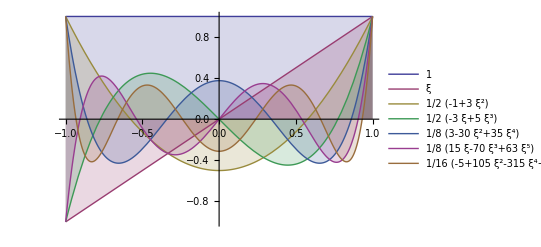

```mathematica
legendreP =Table[LegendreP[i,ξ],{i,0,6}];Table[Subscript[P, i]=legendreP[[i+1]],{i,0,6}];
Plot[Evaluate[legendreP],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

The mass matrix, M, is then defined as

```mathematica
M = Table[∫_-1^1 Subscript[P, i] Subscript[P, j] ⅆξ,{i,0,6},{j,0,6}];M//Simplify//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2/3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2/5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2/7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2/9 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2/11 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2/13)

and

```mathematica
invM = Inverse[M];invM//Simplify//MatrixForm
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 5/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 7/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 9/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 11/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 13/2)

### Stiffness Matrix

```mathematica
Clear[x]; dLegendreP[j_,x_]:= D[LegendreP[j,x], x];
```

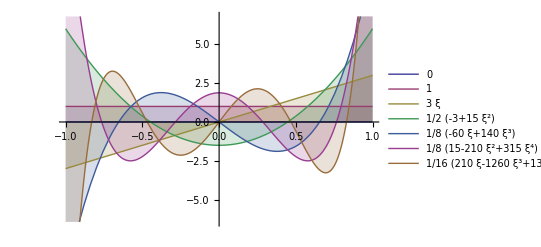

```mathematica
dlegendreP = Table[dLegendreP[i,ξ],{i,0,6}];
Table[Subscript[dP, i]=dLegendreP[i,ξ],{i,0,6}];
Plot[Evaluate[dlegendreP],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
S = Table[∫_-1^1 Subscript[P, i] Subscript[dP, j] ⅆξ,{i,0,6},{j,0,6}];S//Simplify//MatrixForm
```

(0 | 2 | 0 | 2 | 0 | 2 | 0
0 | 0 | 2 | 0 | 2 | 0 | 2
0 | 0 | 0 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 2 | 0 | 2
0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0)

#### Is there any relation between M and S?

Lets explore the case that M = α.S:

```mathematica
Dr = invM.S; Dr //MatrixForm
```

(0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 3 | 0 | 3 | 0 | 3
0 | 0 | 0 | 5 | 0 | 5 | 0
0 | 0 | 0 | 0 | 7 | 0 | 7
0 | 0 | 0 | 0 | 0 | 9 | 0
0 | 0 | 0 | 0 | 0 | 0 | 11
0 | 0 | 0 | 0 | 0 | 0 | 0)

An Amazing relation!

### Vandermonde Matrix

In Nodal DG this is our most important interpolation tool and the key to translate nodal information to legendre coeficients and viceversa. The Vandermonde matrix is defined as,

```mathematica
Vandermonde =  Table[LegendreP[n,Subscript[x, i]],{i,1,5},{n,0,4}]; Vandermonde//MatrixForm
```

(1 | x_1 | 1/2 (-1+3 x_1^2) | 1/2 (-3 x_1+5 x_1^3) | 1/8 (3-30 x_1^2+35 x_1^4)
1 | x_2 | 1/2 (-1+3 x_2^2) | 1/2 (-3 x_2+5 x_2^3) | 1/8 (3-30 x_2^2+35 x_2^4)
1 | x_3 | 1/2 (-1+3 x_3^2) | 1/2 (-3 x_3+5 x_3^3) | 1/8 (3-30 x_3^2+35 x_3^4)
1 | x_4 | 1/2 (-1+3 x_4^2) | 1/2 (-3 x_4+5 x_4^3) | 1/8 (3-30 x_4^2+35 x_4^4)
1 | x_5 | 1/2 (-1+3 x_5^2) | 1/2 (-3 x_5+5 x_5^3) | 1/8 (3-30 x_5^2+35 x_5^4))

where x_i are the nodes coordinates inside our element.
The rules of the game goes as follows:

u_coef = inv[V].u_nodes,   and viceversa     u_nodes = [V].u_coef

It is important to realize that in nodal DG we use Lagrange Polynomials to interpolate data at their respectives nodes (like we do in FEM). How good this interpolation is done? well we rely on the interpolated data from the Legrendre Expansion as the core Idea behind the method.

## Mesh

### Discretization in 1D

Define Domain x ∈ [ a , b ],
We then divide it into ‘n’ small cells/elements

```mathematica
a= 0; b = 1; n = 10; nf = n+1; Δx = (b-a)/n;
```

```mathematica
Table [Subscript[x, i-1/2]=a+ i Δx,{i,0,n}]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

Define Intervals I_j:

```mathematica
Table[Subscript[I, j]={Subscript[x, j-3/2],Subscript[x, j-1/2]},{j,1,n}]
```

{{0,1/10},{1/10,1/5},{1/5,3/10},{3/10,2/5},{2/5,1/2},{1/2,3/5},{3/5,7/10},{7/10,4/5},{4/5,9/10},{9/10,1}}

Define element sizes h_j:

```mathematica
Table[Subscript[h, j]=(Subscript[x, j-1/2]-Subscript[x, j-3/2]),{j,1,n}]
```

{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10}

Define element centers x_j :

```mathematica
Table[Subscript[x, j]=(Subscript[x, j-3/2]+Subscript[x, j-1/2])/2,{j,1,n}]
```

{1/20,3/20,1/4,7/20,9/20,11/20,13/20,3/4,17/20,19/20}

Standar Element Definition I_ξ:

```mathematica
Subscript[I, ξ] = ({{-1, 1}})
```

{{-1,1}}

Therefore the Jacobian metric between this two elements is given by,

```mathematica
J = Subscript[h, j]/2;
```

Now, let us define solution points, ξ_k, inside the standar element:
Lets define a polynomial of degree K=3 on either Legendre / Lobatto points,

```mathematica
K=3;
```

#### Legendre Polynomials

Generating up to 4th degree Legendre Polynomials.

```mathematica
legendreP = Table[LegendreP[i,ξ],{i,0,5}];
```

```mathematica
Table[Subscript[p, i]= legendreP[[i+1]],{i,0,5}];
{Subscript[p, 0],Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4],Subscript[p, 5]}
```

{1,ξ,1/2 (-1+3 ξ^2),1/2 (-3 ξ+5 ξ^3),1/8 (3-30 ξ^2+35 ξ^4),1/8 (15 ξ-70 ξ^3+63 ξ^5)}

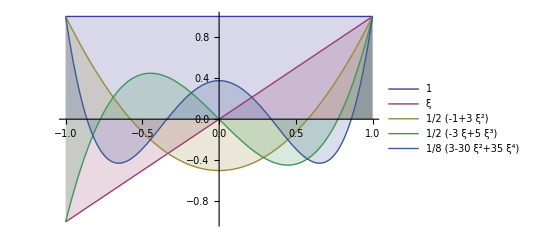

```mathematica
Plot[Evaluate[Most[legendreP]],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

Legendre Roots

```mathematica
abscissas = -Sort[List @@ Roots[Subscript[p, 4]==0,ξ][[All,2]],Greater]
```

{-√(1/35 (15+2 √30)),-√(1/35 (15-2 √30)),√(1/35 (15-2 √30)),√(1/35 (15+2 √30))}

```mathematica
weights={1/36 (18-√30),1/36 (18+√30),1/36 (18+√30),1/36 (18-√30)};
```

#### Legendre-Gauss-Lobatto (LGL) Polynomials

```mathematica
lobatto = Table[Subscript[p, k]-Subscript[p, k-2],{k,2,5}] //Simplify;
```

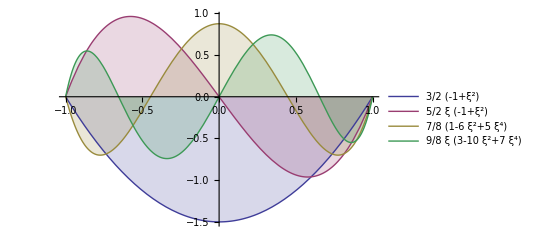

```mathematica
Plot[Evaluate[lobatto],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Table[Subscript[Lo, i]= lobatto[[i]],{i,1,4}]//TableForm
```

3/2 (-1+ξ^2)
5/2 ξ (-1+ξ^2)
7/8 (1-6 ξ^2+5 ξ^4)
9/8 ξ (3-10 ξ^2+7 ξ^4)

Lobatto Roots

```mathematica
abscissas = -Sort[List @@ Roots[Subscript[Lo, 3]==0,ξ][[All,2]],Greater]
```

{-1,-1/(√5),1/(√5),1}

```mathematica
weights={1/6,5/6,5/6,1/6}
```

{1/6,5/6,5/6,1/6}

I, personally, prefer to call the abscissas ‘standard solution points’ or simply ‘solution points’. I will also  referer to all the points inside the domain as my ‘global nodes coordinates’.

```mathematica
{Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]}=abscissas; (* also the local coordinates inside Subscript[I, j] *)
```

Define Subpolynomial Domains over our original Domain. We  define the following mapping for x and ξ (solution points here) :

```mathematica
Subscript[x, 𝒟]=Table[Subscript[x, j]+ J ×abscissas,{j,1,n}];
Subscript[x, 𝒟]//TableForm//N
```

0. | 0.0276393 | 0.0723607 | 0.1
0.1 | 0.127639 | 0.172361 | 0.2
0.2 | 0.227639 | 0.272361 | 0.3
0.3 | 0.327639 | 0.372361 | 0.4
0.4 | 0.427639 | 0.472361 | 0.5
0.5 | 0.527639 | 0.572361 | 0.6
0.6 | 0.627639 | 0.672361 | 0.7
0.7 | 0.727639 | 0.772361 | 0.8
0.8 | 0.827639 | 0.872361 | 0.9
0.9 | 0.927639 | 0.972361 | 1.

Define ' u_(j,k)’ values for every node in our domain.
I will assume an IC as: u0(x) = 0.5 +sin(2πx), therefore

```mathematica
Table[Subscript[x, j,k]= Subscript[x, 𝒟][[j,k]],{j,1,n},{k,1,4}];
```

```mathematica
u0[x_]:=0.5+Sin[2 π x]; (* or *)
u0[x_]:= Piecewise[{{2,x<=0.45},{1,x>0.45}}];
Subscript[u, 𝒟] = Table[u0[Subscript[x, j,k]],{j,1,10},{k,1,4}];
Subscript[u, 𝒟]//TableForm
```

2 | 2 | 2 | 2
2 | 2 | 2 | 2
2 | 2 | 2 | 2
2 | 2 | 2 | 2
2 | 2 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1

Load u_0 into our domain

```mathematica
Table[Subscript[u, j,k]= Subscript[u, 𝒟][[j,k]],{j,1,n},{k,1,4}];
```

take for example j=4 and k=1, we should get

```mathematica
Subscript[u, 4,1]
```

2

#### Continuous Case

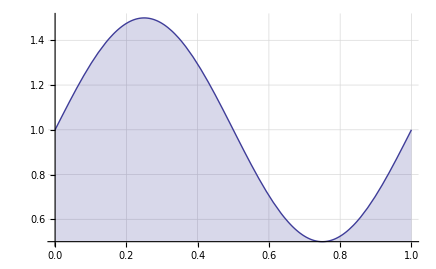

```mathematica
u[x_,t_]:= 0.5(2+Sin[2π x]);
sin =Plot[u[x,t],{x,0,1},PlotRange->Full,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],Filling->Axis]
```

#### Discontinuous Case

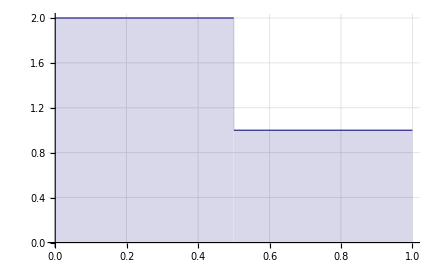

```mathematica
u[x_,t_]:= Piecewise[{{2,x<0.5},{1,x>=0.5}}]
Plot[u[x,t],{x,0,1},PlotRange->{0,2},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],Filling->Axis]
```

Assume t = 0. Evaluate u[x, t] at discrete value points,

## Legendre coeficients, u_j^(i)(t), ←2→ nodal data, u^h(x,t)

Here we are interested in understanding the expansion of these polynomials from a continuous form to a pieze wize for of the from.

### Initialization

#### Build Notation

```mathematica
Symbolize[Subscript[u, h]];Symbolize[u^_];
```

```mathematica
Subscript[u, 1]//InputForm
```

Subscript[u, 1]

```mathematica
u^(l) // InputForm
```

u⎵Superscript⎵LeftParenthesis⎵l⎵RightParenthesis

```mathematica
Table[ToExpression[RowBox[{"{",ToString[i],"}"}]],{i,10}]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}

```mathematica
Notation[∫_Subscript[I, j] f_ⅆx_ ⟹ Integrate[f_,{x_,-Subscript[Δx, j]/2,Subscript[Δx, j]/2}]]
```

#### Case1: assume the Riemann IC:

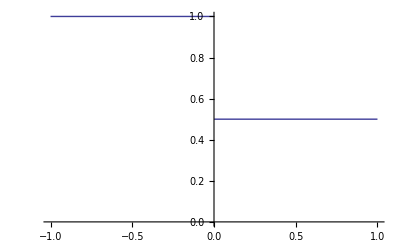

```mathematica
u[x_,t_]:= Piecewise[{{1,x<0},{0.5,x>=0}}];
Plot[u[x,t],{x,-1,1},PlotRange->{0,1}]
```

#### Case2: assume Sinusoidal wave function :

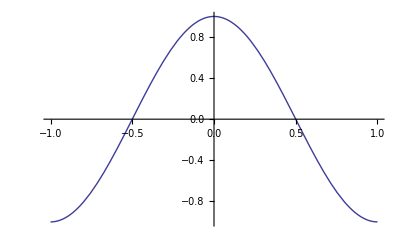

```mathematica
u[x_,t_]:= Cos[π x];
Plot[u[x,t],{x,-1,1},PlotRange->Full]
```

### Method 1: Traditional Way

#### Degrees of Freedom u_j^(l)

For u_j element using the continuous function u(x,t). If we define the degrees of freedom as:

u_j^(l) = u_j^(l)[t] = 1/Δx_j^(l+1)∫_I_j u[x,t] v_l^(j)[x]ⅆx, for l = 1,...,k

of course, we need to define u[x,t] in order to continue. We traditionally have two choises a continuous or a discontinuous function,

Therefore :

```mathematica
{u^(0),u^(1),u^(2),u^(3),u^(4),u^(5),u^(6)} = Table[ 1/Subscript[Δx, j]^(l+1)∫_Subscript[I, j] (u[x,t] Subscript[v, l])ⅆx,{l,0,6}];
```

```mathematica
{u^(0),u^(1),u^(2),u^(3),u^(4),u^(5),u^(6)} //MatrixForm
```

(0.75
-0.0625
0.
0.0015625
0.
-0.000062004
0.)

#### Solution Approximation u_h

```mathematica
Quit[];
```

And the approximation of the solution u(x,t) as u_h, is defined as follows

u^h[x,t] = ∑_(l=0)^k a_l u_j^(l)[t]v_l^(j)[x], for x ∈ I_j

here a_l are contants values found to normalize the contribution of each polinomial.

for the Modal formulation the expasion is of the form

```mathematica
Np = 4;
ClearAll[sum]
```

```mathematica
sum[x_,t_,n_Integer?Positive]:=Array[Subscript[u[t], #] Subscript[v[x], #]&,n,1,Defer[Plus[##]]&]
```

```mathematica
Subscript[u, h][x_,t_] := sum[x,t,Np]
```

```mathematica
Subscript[u, h][a,b]
```

u[b]_1 v[a]_1+u[b]_2 v[a]_2+u[b]_3 v[a]_3+u[b]_4 v[a]_4

for the Nodal formulation the expansion is of the form

```mathematica
Np = 5;
ClearAll[sum]
```

```mathematica
sum[x_,t_,n_Integer?Positive]:=Array[Subscript[u[x,t], #] Subscript[v[x], #]&,n,1,Defer[Plus[##]]&]
```

```mathematica
Subscript[u, h][x_,t_] := sum[x,t,Np]
```

```mathematica
Subscript[u, h][a,b]
```

u[a,b]_1 v[a]_1+u[a,b]_2 v[a]_2+u[a,b]_3 v[a]_3+u[a,b]_4 v[a]_4+u[a,b]_5 v[a]_5

Following the last example we can proceed to compute from the degress of freedom the approximate solution u_h,

```mathematica
NSum[Subscript[a, l] u^(l)Subscript[v, l],{l,0,3}]
```

### Method 2: The Vandermonde Matrix

#### Degrees of Freedom u_j^(l)

From previous calculations we can do:

```mathematica
Table[Subscript[v, i]= Expand[Subscript[p, i]],{i,0,6}];(* recall that z -> (x-Subscript[x, j])/Subscript[Δx, j] *)
Table[Subscript[v, i],{i,0,6}]//MatrixForm
```

(1
z
-1/12+z^2
-(3 z)/20+z^3
3/560-(3 z^2)/14+z^4
(5 z)/336-(5 z^3)/18+z^5
-5/14784+(5 z^2)/176-(15 z^4)/44+z^6)

Evaluating every escaled polynomial for the computed abcsissas we get:

```mathematica
vandermonde = Table[Subscript[v, n]/.z->Subscript[x, m],{m,1,4},{n,0,3}];
vandermonde //MatrixForm
```

(1 | 1/3 | 1/36 | -7/540
1 | 1/2+1/(6 √5) | -1/12+(1/2+1/(6 √5))^2 | -3/20 (1/2+1/(6 √5))+(1/2+1/(6 √5))^3
1 | 1/2-1/(6 √5) | -1/12+(1/2-1/(6 √5))^2 | -3/20 (1/2-1/(6 √5))+(1/2-1/(6 √5))^3
1 | 2/3 | 13/36 | 53/270)

if for the case every we are using equally distributed cells, we can just program the numerical version of this matrix:

```mathematica
vandermonde //MatrixForm//N
```

(1. | 0.333333 | 0.0277778 | -0.012963
1. | 0.574536 | 0.246758 | 0.103469
1. | 0.425464 | 0.0976866 | 0.0131979
1. | 0.666667 | 0.361111 | 0.196296)

#### Solution Approximation u_h